```mathematica
ClearAll["Global`*"]
```

```mathematica
(*System properties*)
G = 6.674*10^(-11);
Mearth = 5.972*10^24;
mu = G*Mearth;
Rearth = 6371000;

(*Initial Conditions*)
R1 = Rearth + 322000 ;(*Starting orbit, in meters*)
R2 = Rearth +35786000 ;(*Target orbit, in meters*)
TOF =12000; (*Time of flight, in seconds*)

(*Compute properties of Hohman transfer eclipse (used as search conditions)*)
a1 =(R1+R2)/2;
e1 = (a1-R1)/a1;
```

```mathematica
(*Setup system of equations *)
eq1 = TOF==Sqrt[a^3/mu]*(Eb-(e*Sin[Eb]));
eq2 =R2 == a*(1-(e*Cos[Eb]));
eq3 = Cos[ni]==(Cos[Eb]-e)/(1-e*Cos[Eb]);
eq4 = Sin[ni]==Sqrt[1-e^2]*Sin[Eb]/(1-e*Cos[Eb]);

{atransfer,etransfer,nitransfer}={a,e,ni} /.FindRoot[{eq1,eq2,eq3,eq4},{Eb,1.7},{a, a1,a1,Infinity},{e,e1},{ni,3},AccuracyGoal->10]
```

{3.04871×10^7,0.769882,2.7296}

```mathematica
(*Compute non-tangential maneuver velocities *)
vc1 = Sqrt[mu/R1];
vc2 = Sqrt[mu/R2];
va = Sqrt[(mu/atransfer)*((1+etransfer)/(1-etransfer))];
Deltav1 = va-vc1;
vb = Sqrt[mu*((2/R2)-(1/atransfer))];
cosphi=(R1*va)/(R2*vb);
phi = ArcCos[cosphi]/Degree;
Deltav2 = Sqrt[vc2^2+vb^2-(2vc2*vb*cosphi)];
Print["DV1 = ",Deltav1," m/s"]
Print["DV2 = ", Deltav2," m/s"]
Print["phi = ", phi, " degrees"]
Print["Total impulse DV = ",Deltav1+Deltav2," m/s"]
```

DV1 = 2310.59 m/s

DV2 = 2345.14 m/s

phi = 48.7739 degrees

Total impulse DV = 4655.74 m/s

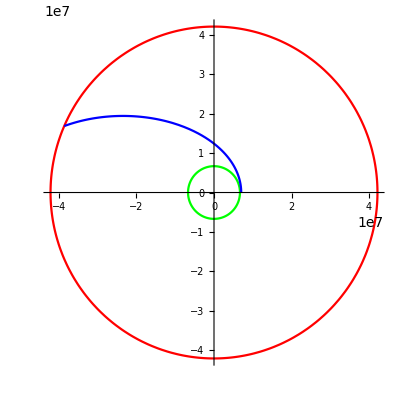

```mathematica
(*Plot the maneuver*)
r[θ_,a_,e_]:=(a*(1-e^2))/(1+e Cos[θ])
orbit1= PolarPlot[r[θ,R1,0], {θ,0, 2 Pi},PlotStyle->Green, AspectRatio->Automatic];
orbit2= PolarPlot[r[θ,R2,0], {θ,0, 2 Pi},PlotStyle->Red, AspectRatio->Automatic];
orbit3= PolarPlot[r[θ, atransfer,etransfer], {θ,0, nitransfer},PlotStyle->Blue, AspectRatio->Automatic];
Show[orbit1,orbit2,orbit3]
```